```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
R=1;
L=1;
```

```mathematica
k[m_,n_]:= BesselJZero[m,n]/R;
```

```mathematica
Ez[r_,θ_,z_,m_,n_,p_]:=BesselJ[m,k[m,n]*r]* Cos[m θ] Cos[(p π z)/L];
```

```mathematica
zyl r[x_,y_,z_]:= Sqrt[x^2+y^2];
zyl θ[x_,y_,z_]:=ArcTan[x,y];
zyl z[x_,y_,z_]:=z;
```

```mathematica
z=0.5;
m=2;
n=1;
p=0;
```

```mathematica
max[z_,m_,n_,p_]:=NMaxValue[
{Ez[zyl r[x,y,z], zyl θ[x,y,z], zyl z[x,y,z],m,n,p],
{x,y}∈Disk[{0,0},1]},{x,y}];
min[z_,m_,n_,p_]:=NMinValue[{Ez[zyl r[x,y,z], zyl θ[x,y,z], zyl z[x,y,z],m,n,p],
{x,y}∈Disk[{0,0},1]},{x,y}];

maxval = max[z,m,n,p];
minval = min[z,m,n,p];
val = Max[Abs[maxval],Abs[minval]];
```

```mathematica
ColorFunc[z_]:=ColorData["LightTemperatureMap","ColorFunction"][Rescale[z,{-val, val}]]
```

```mathematica
plt[z_,m_,n_,p_]:=DensityPlot[Ez[zyl r[x,y,z], zyl θ[x,y,z], zyl z[x,y,z],m,n,p],{x,y}∈Disk[{0,0},1],Epilog->{Thick,Circle[]},PlotTheme->"Scientific",PlotRange->{-val,val},ColorFunction->ColorFunc,ColorFunctionScaling->False,Mesh->None,PlotPoints->40,PlotLegends->BarLegend[Automatic,LegendMarkerSize->220,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"Ε_z",LabelStyle-> Directive[FontSize->26]],Frame->False,PlotRangePadding->0.04];
```

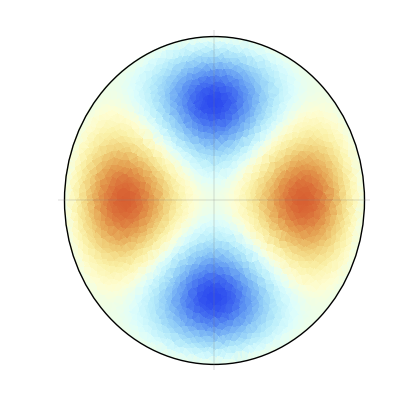

```mathematica
plt 1=plt[z,m,n,p]
```

```mathematica
Export["tm210.pdf", plt 1,"AllowRasterization"->True, ImageSize->360,ImageResolution->600];
```